```mathematica
(* P3: Variational analysis of x⁴ potential: Shooting method *)
```

```mathematica
(* Part a *)
```

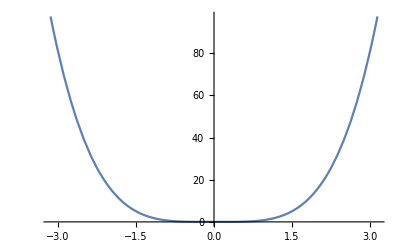

```mathematica
V[x_] := α x^4
Plot[V[x] /. α -> 1, {x, -π, π}]
```

```mathematica
Ĥ[f_] := -ℏ^2/(2m) D[f, {x, 2}] + V[x] f
```

```mathematica
β = (ℏ^2/(m α))^(1/6)
```

(ℏ^2/(m α))^(1/6)

```mathematica
Solve[e == m β^2 EE/ℏ^2, EE]
```

{{EE→(e ℏ^2)/(m (ℏ^2/(m α))^(1/3))}}

```mathematica
Simplify[%]
```

{{EE→e α (ℏ^2/(m α))^(2/3)}}

```mathematica
(* i.e. EE -> e((ℏ^4 α)/m^2)^(1/3)
```

```mathematica
(* Part b *)
```

```mathematica
Shooting[diffeqn_, ics_, depvar_, indepvar_, param_, range_] := Module[{tol = 10^-6, step=0.01, result=1, oldresult=1, value=range[[1]],evalpoint=range[[2]]},
While[Abs[result]>tol,
Print[value, " ", result];
depvar=.;
depvar=depvar/.NDSolve[Join[{diffeqn}, ics]/.param->value, depvar, Join[{indepvar}, range]][[1]];
result = depvar[evalpoint];
value = value + If[result>0, step, -step];
 step = step / If [Sign[result] != Sign[oldresult], 2, 1];
 oldresult = result;
];
depvar=.;
value
];
```

```mathematica
Shooting[-1/2 ψ''[u]+(u^4-e)ψ[u] == 0, {ψ[0] == 1, ψ'[0] == 0}, ψ, u, e,{0, 3}]
```

0 1

0.01 58441.2

0.02 57171.8

0.03 55916.7

0.04 54675.8

0.05 53449.

0.06 52236.1

0.07 51037.

0.08 49851.7

0.09 48679.9

0.1 47521.7

0.11 46376.7

0.12 45245.1

0.13 44126.6

0.14 43021.1

0.15 41928.6

0.16 40848.8

0.17 39781.8

0.18 38727.4

0.19 37685.5

0.2 36655.9

0.21 35638.6

0.22 34633.5

0.23 33640.5

0.24 32659.4

0.25 31690.2

0.26 30732.8

0.27 29787.

0.28 28852.8

0.29 27930.1

0.3 27018.7

0.31 26118.5

0.32 25229.6

0.33 24351.7

0.34 23484.7

0.35 22628.7

0.36 21783.4

0.37 20948.8

0.38 20124.8

0.39 19311.3

0.4 18508.2

0.41 17715.4

0.42 16932.9

0.43 16160.4

0.44 15398.1

0.45 14645.6

0.46 13903.1

0.47 13170.3

0.48 12447.2

0.49 11733.7

0.5 11029.7

0.51 10335.1

0.52 9649.92

0.53 8973.97

0.54 8307.2

0.55 7649.53

0.56 7000.86

0.57 6361.13

0.58 5730.24

0.59 5108.12

0.6 4494.69

0.61 3889.87

0.62 3293.57

0.63 2705.73

0.64 2126.25

0.65 1555.08

0.66 992.116

0.67 437.299

0.66 -109.452

0.665 437.299

0.6675 162.921

0.67 26.4841

0.6675 -109.452

0.66875 26.4841

0.668125 -41.5469

0.667813 -7.54706

0.668125 9.4646

0.667969 -7.54706

0.668047 0.957789

0.668008 -3.29491

0.667988 -1.16865

0.667969 -0.105458

0.667988 0.957789

0.667979 -0.105458

0.667983 0.426171

0.667986 0.160356

0.667988 0.0274546

0.667986 -0.105458

0.667987 0.0274546

0.667986 -0.039002

0.667986 -0.00577254

0.667986 0.0108414

0.667986 -0.00577254

0.667986 0.00253469

0.667986 -0.00161885

0.667986 0.000457971

0.667986 -0.000580297

0.667986 -0.0000613564

0.667986 0.000198378

0.667986 -0.0000613564

0.667986 0.0000686027

0.667986 3.66732×10^-6

0.667986 -0.0000288231

0.667986 3.66732×10^-6

0.667986 -0.000012581

0.667986 -4.45385×10^-6

0.667986